## Misc Functions

```mathematica
Welch=ResourceFunction["WelchSpectralEstimate"];
```

## Load Data

```mathematica
files=FileNames[FileNameJoin[{NotebookDirectory[],"NoiseFloors","*.bin"}]]
rate=10*10^6;
raw=ParallelTable[{
First@StringCases[ff,"ULNLDD-"~~output:Repeated[WordCharacter]~~"-"~~modType:Repeated[WordCharacter]~~"-NF_":>{output,modType}],
BinaryReadList[ff,"Real32"]
},{ff,files}];
```

{\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-100u-AC-NF_20261105_112133.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-100u-DC-NF_20261105_111741.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-100u-JFET-NF_20261105_115240.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-10u-AC-NF_20261104_180533.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-10u-DC-NF_20261104_180923.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-10u-JFET-NF_20261104_173706.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-150u-AC-NF_20261105_141138.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-150u-DC-NF_20261105_140737.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-150u-JFET-NF_20261105_122110.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-Direct-AC-NF_20261104_161251.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-Direct-DC-NF_20261104_160824.bin,\\qomsa.physik.hu-berlin.de\QOM_SHARE\projects\ROSC\Data\Thematic Structure\ULNLDD_v0_3\Modulation\NoiseFloors\ULNLDD-Direct-JFET-NF_20261104_165055.bin}

```mathematica
segmentSize=4096;
psds=ParallelTable[{rr[[1]],Welch[rr[[2]],rate,"SegmentSize"->segmentSize]},{rr,raw}];
asds=ParallelTable[{ppsds[[1]],Transpose[{ppsds[[2,2;;-2,1]],Sqrt[ppsds[[2,2;;-2,2]]]}]},{ppsds,psds}];
```

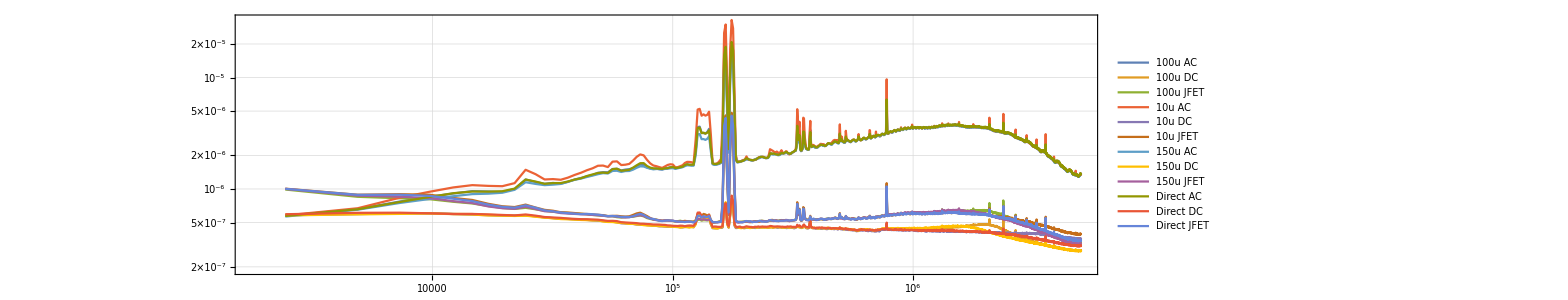

```mathematica
ListLogLogPlot[asds[[All,-1]],
Joined->True,PlotRange->All,GridLines->Full,
PlotStyle->(ColorData[97,#]&/@Range[Length[asds]]),
PlotLegends->((#1<>" "<>#2)&@@@asds[[All,1]]),
ImageSize->1200,AspectRatio->1/4
]
```

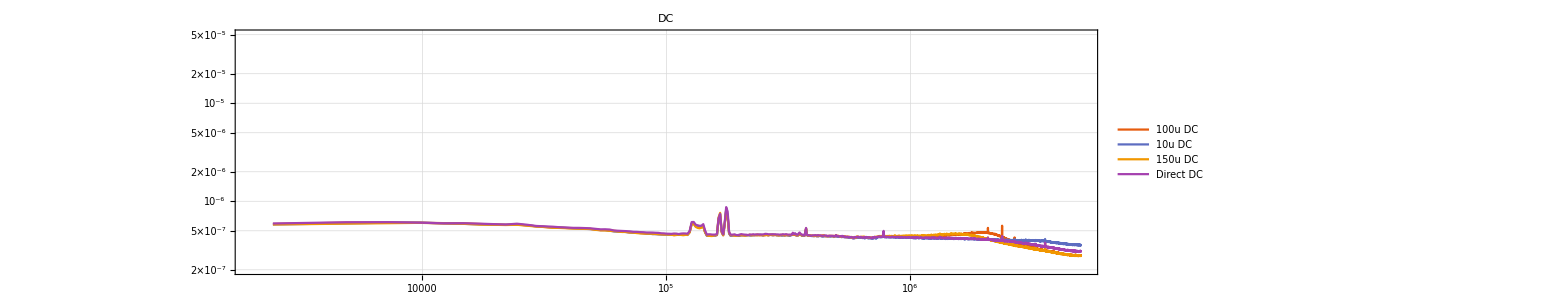

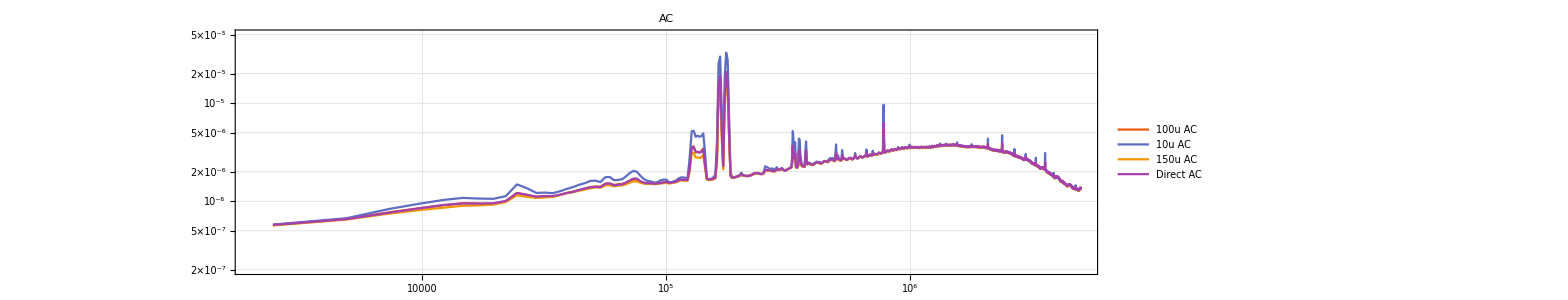

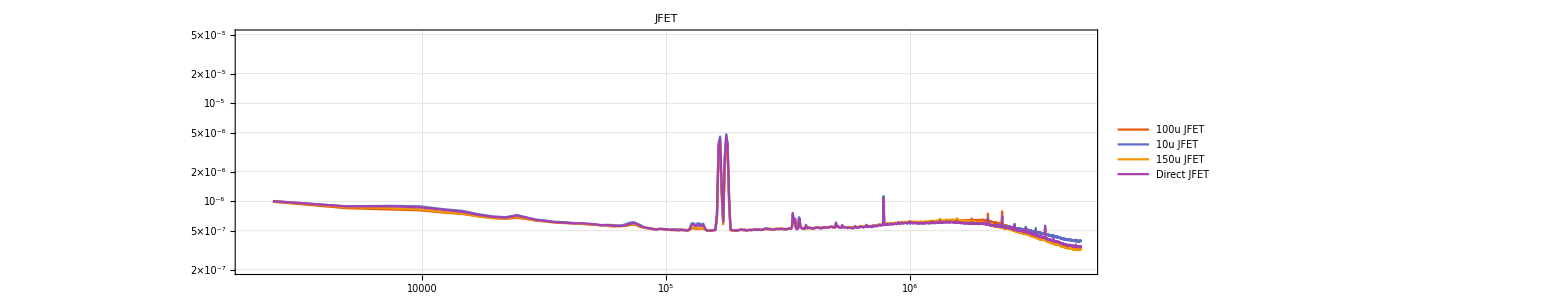

```mathematica
asdsDC=Select[asds,#[[1,2]]=="DC"&];
gPlotRange={{2000,5*10^6},{2*10^-7,5*10^-5}};
ListLogLogPlot[asdsDC[[All,-1]],
Joined->True,PlotRange->gPlotRange,GridLines->Full,PlotLabel->"DC",
PlotLegends->((#1<>" "<>#2)&@@@asdsDC[[All,1]]),
ImageSize->1200,AspectRatio->1/4
]
asdsAC=Select[asds,#[[1,2]]=="AC"&];
ListLogLogPlot[asdsAC[[All,-1]],
Joined->True,PlotRange->gPlotRange,GridLines->Full,PlotLabel->"AC",
PlotLegends->((#1<>" "<>#2)&@@@asdsAC[[All,1]]),
ImageSize->1200,AspectRatio->1/4
]
asdsJFET=Select[asds,#[[1,2]]=="JFET"&];
ListLogLogPlot[asdsJFET[[All,-1]],
Joined->True,PlotRange->gPlotRange,GridLines->Full,PlotLabel->"JFET",
PlotLegends->((#1<>" "<>#2)&@@@asdsJFET[[All,1]]),
ImageSize->1200,AspectRatio->1/4
]
```